```mathematica
tau1 = Function[t,2.  Sin[0.5 t]]
tau2 = Function[t,  1.5 Cos[1.5 t]] (*check equations*) 
eqsDoublePend = {tau2[t] == 0.3333 m2 l^2 x1''[t] + 0.3333 m2 l x2''[t] + 0.5 m2 l^2 Cos[x2[t]] x1''[t] + 0.5 m2 g l Cos[x1[t] + x2[t]] + 0.5 m2 l^2 Sin[x2[t]] x1'[t]^2 , tau1[t] ==  0.3333 m1 l^2 x1''[t] +1.3333 m2 l x1''[t] +0.3333 m2 l x2''[t] + m2 Cos[x2[t]] l^2 x1''[t] + 0.5 m2 l^2 Cos[x2[t]] x2''[t] - m2 Sin[x2[t]] l^2 x1'[t] x2'[t] - 0.5 m2 Sin[x2[t]] l^2 (x2'[t])^2 + 0.5 m1 g l Cos[x1[t]] + 0.5 m2 g l Cos[x1[t] + x2[t]] + m2 g l Cos[x1[t]]}
```

Function[t,2. Sin[0.5 t]]

Function[t,1.5 Cos[1.5 t]]

{1.5 Cos[1.5 t]==0.5 g l m2 Cos[x1[t]+x2[t]]+0.5 l^2 m2 Sin[x2[t]] x1'[t]^2+0.3333 l^2 m2 x1''[t]+0.5 l^2 m2 Cos[x2[t]] x1''[t]+0.3333 l m2 x2''[t],2. Sin[0.5 t]==0.5 g l m1 Cos[x1[t]]+g l m2 Cos[x1[t]]+0.5 g l m2 Cos[x1[t]+x2[t]]-l^2 m2 Sin[x2[t]] x1'[t] x2'[t]-0.5 l^2 m2 Sin[x2[t]] x2'[t]^2+0.3333 l^2 m1 x1''[t]+1.3333 l m2 x1''[t]+l^2 m2 Cos[x2[t]] x1''[t]+0.3333 l m2 x2''[t]+0.5 l^2 m2 Cos[x2[t]] x2''[t]}

```mathematica
rules = {m1->1., m2->1., l->1., g->9.81}
```

{m1→1.,m2→1.,l→1.,g→9.81}

```mathematica
ndsol = NDSolve[(eqsDoublePend/.rules)~Join~{x1[0]==0 Degree,x2[0] == 0 Degree,x1'[0]==0, x2'[0] == 0},{x1[t], x2[t], x1'[t], x2'[t]},{t, 0, 10}][[1]]
```

{x1[t]→InterpolatingFunction[…][t],x2[t]→InterpolatingFunction[…][t],x1'[t]→InterpolatingFunction[…][t],x2'[t]→InterpolatingFunction[…][t]}

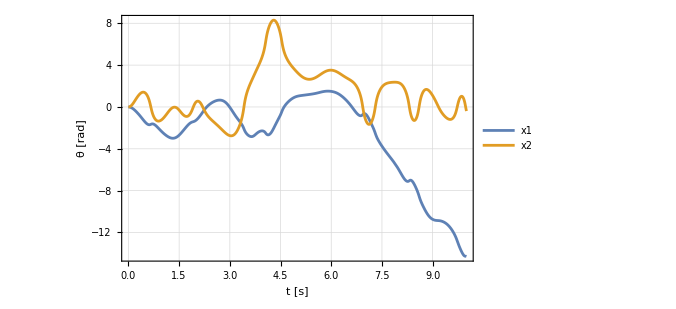

```mathematica
Plot[Evaluate[{x1[t], x2[t]}/.ndsol],{t,0,10},Frame->True,GridLines->Automatic,LabelStyle->Directive[20, Black],ImageSize->500,FrameLabel->{"t [s]","θ [rad]"}, PlotLegends->{"x1", "x2"}]
```

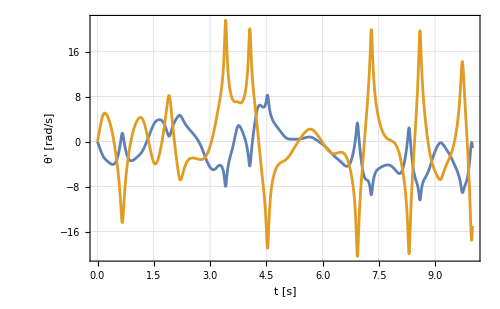

```mathematica
Plot[Evaluate[{x1'[t], x2'[t]}/.ndsol],{t,0,10},Frame->True,GridLines->Automatic,LabelStyle->Directive[20, Black],ImageSize->500,FrameLabel->{"t [s]","θ' [rad/s]"}]
```

```mathematica
doubles = Solve[eqsDoublePend, {x1''[t], x2''[t]}]/.rules/.ndsol
```

{{x1''[t]→-((-1. (-0.3333-0.5 Cos[InterpolatingFunction[…][t]]) (1.5 Cos[1.5 t]-4.905 Cos[InterpolatingFunction[…][t]+InterpolatingFunction[…][t]]-0.5 Sin[InterpolatingFunction[…][t]] (InterpolatingFunction[…][t])^2)-0.3333 (-14.715 Cos[InterpolatingFunction[…][t]]-4.905 Cos[InterpolatingFunction[…][t]+InterpolatingFunction[…][t]]+2. Sin[0.5 t]+1. Sin[InterpolatingFunction[…][t]] InterpolatingFunction[…][t] InterpolatingFunction[…][t]+0.5 Sin[InterpolatingFunction[…][t]] (InterpolatingFunction[…][t])^2))/(0.444389-0.25 Cos[InterpolatingFunction[…][t]]^2)),x2''[t]→(2. (-4.9998 Cos[1.5 t]-9.80902 Cos[InterpolatingFunction[…][t]]-3. Cos[1.5 t] Cos[InterpolatingFunction[…][t]]-14.715 Cos[InterpolatingFunction[…][t]] Cos[InterpolatingFunction[…][t]]+13.0797 Cos[InterpolatingFunction[…][t]+InterpolatingFunction[…][t]]+4.905 Cos[InterpolatingFunction[…][t]] Cos[InterpolatingFunction[…][t]+InterpolatingFunction[…][t]]+1.3332 Sin[0.5 t]+2. Cos[InterpolatingFunction[…][t]] Sin[0.5 t]+1.6666 Sin[InterpolatingFunction[…][t]] (InterpolatingFunction[…][t])^2+1. Cos[InterpolatingFunction[…][t]] Sin[InterpolatingFunction[…][t]] (InterpolatingFunction[…][t])^2+0.6666 Sin[InterpolatingFunction[…][t]] InterpolatingFunction[…][t] InterpolatingFunction[…][t]+1. Cos[InterpolatingFunction[…][t]] Sin[InterpolatingFunction[…][t]] InterpolatingFunction[…][t] InterpolatingFunction[…][t]+0.3333 Sin[InterpolatingFunction[…][t]] (InterpolatingFunction[…][t])^2+0.5 Cos[InterpolatingFunction[…][t]] Sin[InterpolatingFunction[…][t]] (InterpolatingFunction[…][t])^2))/(-1.77756+1. Cos[InterpolatingFunction[…][t]]^2)}}

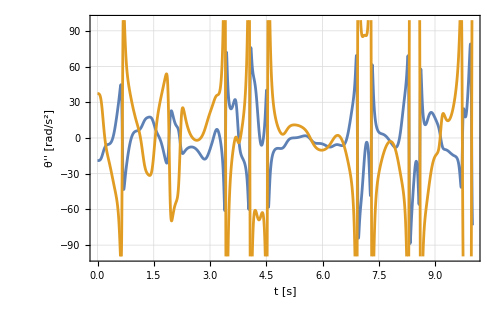

```mathematica
Plot[Evaluate[{x1''[t], x2''[t]}/.doubles],{t,0,10},Frame->True,GridLines->Automatic,LabelStyle->Directive[20, Black],ImageSize->500,FrameLabel->{"t [s]","θ'' [rad/s^2]"}]
```

```mathematica
ClearAll@results
results[sols_, time_, expr_] := Module[{sol, sol2, solF},
sol = sols/.t->time;
sol2 = expr/.t->time;
solF = Join[sol[[All, 2]], sol2[[1, All, 2]]];
solF]
```

```mathematica
var = ndsol/.t->0.5
```

{x1[0.5]→-1.46578,x2[0.5]→1.33217,x1'[0.5]→-3.43225,x2'[0.5]→-2.75668}

```mathematica
var[[All, 2]]
```

{-1.46578,1.33217,-3.43225,-2.75668}

```mathematica
var2 = doubles/.t->0.5
```

{{x1''[0.5]→15.3536,x2''[0.5]→-49.2617}}

```mathematica
var2[[1, All, 2]]
```

{15.3536,-49.2617}

```mathematica
sol1 = results[ndsol, 0.5, doubles]
```

{-1.46578,1.33217,-3.43225,-2.75668,15.3536,-49.2617}

```mathematica
finalRes = Table[{time,results[ndsol,time, doubles]},{time,0., 10., 10./1000.}]
```

```mathematica
ndsol/.t->10
```

{x1[10]→-14.2833,x2[10]→-0.390936,x1'[10]→-1.16266,x2'[10]→-15.0149}

```mathematica
doubles/.t->10
```

{{x1''[10]→-73.3328,x2''[10]→179.926}}

```mathematica
Length@finalRes[[All, 2]]
```

1001

```mathematica
finalRes[[1]]
```

{0.,{0.,0.,-2.71051×10^-20,0.,-19.0441,37.3971}}

```mathematica
Short@finalRes[[All, 2]]
```

{{0.,0.,-2.71051×10^-20,0.,-19.0441,37.3971},«999»,{-14.2833,-0.390936,-«18»,-«19»,-73.3328,179.926}}

```mathematica
Export["A:\\uni\\masters nu\\RA\\pythonCode\\data\\planarDoublePend.csv",finalRes[[All, 2]]]
```

A:\uni\masters nu\RA\pythonCode\data\planarDoublePend.csv

```mathematica
Import[%]
```

```mathematica
Directory[]
```

C:\Users\alizhan